## Search

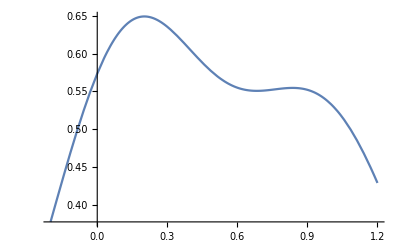

0.55132

-0.25

```mathematica
(*razoring*)
Table[1810-(530 + 20*x), {x,1, 64}]//MatrixForm;

(*Time allocation*)

(*Plot[1.125gauss[0.125,0.135]+1.125gauss[0.96,0.15],{x,0,1}]*)
gauss[μ_,σ_,x_]:=1/(Sqrt[2π σ])*Exp[-(μ-x)^2/(2σ)]
tot=Re[Integrate[1.125gauss[0.125,0.135]+1.125gauss[0.96,0.15],{x,-∞,∞}]];
f1[x_]:=1./tot(1.125gauss[0.125,0.115,x]+1.125gauss[0.96,0.15,x])
Plot[f1[x],{x,-0.2,1.2}]

timeMS=10000;
incMS=6000;
totMS=timeMS+incMS;
moves=45-30;
timePerMove=2.5*totMS / moves;
f1[0.65]
```

## Evaluation

```mathematica
(*Mobility middlegame (knight, bishop, rook, queen)*)
Table[-50 + 100/7 * x//N, {x,0,7}]//MatrixForm;
Table[-75 + 150/12 * x//N, {x,0,12}]//MatrixForm;
Table[-60 + 120/13 * x//N, {x,0,13}]//MatrixForm;
Table[-30 + 60/(27)*x//N, {x, 0, 27}]//MatrixForm;

kc=50/12*2//N;
bc=75/18*2//N;
rc=60/54//N;
qc=60/27//N;
Table[-2+kc*Log[x+1]//N,{x,0,7}]//MatrixForm;
Table[-2+bc*Log[x+1]//N,{x,0,12}]//MatrixForm;
Table[-0+rc*Log[x+1]//N,{x,0,13}]//MatrixForm;
Table[-0+qc*Log[x+1]//N,{x,0,27}]//MatrixForm;
```

```mathematica
(*Attack tables middlegame (knight, bishop, rook, queen)*)
bases={3.0, 3.0, 1.5, 0.75};
multipliers={1.0, 3.0, 3.15, 4.80, 9.10};
Table[bases[[1]]*multipliers[[i]],{i,1,5}]
Table[bases[[2]]*multipliers[[i]],{i,1,5}]
Table[bases[[3]]*multipliers[[i]],{i,1,5}]
Table[bases[[4]]*multipliers[[i]],{i,1,5}]
```

{3.,9.,9.45,14.4,27.3}

{3.,9.,9.45,14.4,27.3}

{1.5,4.5,4.725,7.2,13.65}

{0.75,2.25,2.3625,3.6,6.825}

2666.67